{{1,15,1,15,1},{2,14,2,15,1},{3,13,3,15,1},{4,12,4,13,1},{4,14,4,14,0},{4,15,4,15,1},{5,11,5,15,1},{6,10,6,11,1},{6,12,6,14,0},{6,15,6,15,1},{7,9,7,11,1},{7,12,7,13,0},{7,14,7,15,1},{8,8,8,9,1},{8,10,8,10,0},{8,11,8,11,1},{8,12,8,12,0},{8,13,8,15,1},{9,7,9,13,1},{9,14,9,14,0},{9,15,9,15,1},{10,6,10,7,1},{10,8,10,12,0},{10,13,10,15,1},{11,5,11,7,1},{11,8,11,11,0},{11,12,11,13,1},{11,14,11,14,0},{11,15,11,15,1},{12,4,12,5,1},{12,6,12,6,0},{12,7,12,7,1},{12,8,12,10,0},{12,11,12,15,1},{13,3,13,7,1},{13,8,13,9,0},{13,10,13,11,1},{13,12,13,14,0},{13,15,13,15,1},{14,2,14,3,1},{14,4,14,6,0},{14,7,14,7,1},{14,8,14,8,0},{14,9,14,11,1},{14,12,14,13,0},{14,14,14,15,1},{15,2,15,3,1},{15,4,15,5,0},{15,6,15,9,1},{15,10,15,10,0},{15,11,15,11,1},{15,12,15,12,0},{15,13,15,15,1},{16,2,16,3,1},{16,4,16,4,0},{16,5,16,6,1},{16,7,16,8,0},{16,9,16,13,1},{16,14,16,14,0},{16,15,16,15,1},{17,2,17,6,1},{17,7,17,7,0},{17,8,17,9,1},{17,10,17,12,0},{17,13,17,15,1},{18,2,18,2,1},{18,3,18,5,0},{18,6,18,9,1},{18,10,18,11,0},{18,12,18,13,1},{18,14,18,14,0},{18,15,18,15,1},{19,2,19,2,1},{19,3,19,4,0},{19,5,19,6,1},{19,7,19,8,0},{19,9,19,9,1},{19,10,19,10,0},{19,11,19,15,1},{20,2,20,2,1},{20,3,20,3,0},{20,4,20,6,1},{20,7,20,7,0},{20,8,20,11,1},{20,12,20,14,0},{20,15,20,15,1},{21,2,21,4,1},{21,5,21,5,0},{21,6,21,8,1},{21,9,21,10,0},{21,11,21,11,1},{21,12,21,13,0},{21,14,21,15,1},{22,2,22,2,1},{22,3,22,3,0},{22,4,22,6,1},{22,7,22,7,0},{22,8,22,8,1},{22,9,22,9,0},{22,10,22,11,1},{22,12,22,12,0},{22,13,22,15,1},{23,2,23,4,1},{23,5,23,5,0},{23,6,23,13,1},{23,14,23,14,0},{23,15,23,15,1},{24,2,24,2,1},{24,3,24,3,0},{24,4,24,6,1},{24,7,24,12,0},{24,13,24,15,1},{25,2,25,4,1},{25,5,25,5,0},{25,6,25,6,1},{25,7,25,11,0},{25,12,25,13,1},{25,14,25,14,0},{25,15,25,15,1},{26,2,26,2,1},{26,3,26,3,0},{26,4,26,6,1},{26,7,26,10,0},{26,11,26,15,1},{27,2,27,4,1},{27,5,27,5,0},{27,6,27,6,1},{27,7,27,9,0},{27,10,27,11,1},{27,12,27,14,0},{27,15,27,15,1},{28,2,28,2,1},{28,3,28,3,0},{28,4,28,6,1},{28,7,28,8,0},{28,9,28,11,1},{28,12,28,13,0},{28,14,28,15,1},{29,2,29,4,1},{29,5,29,5,0},{29,6,29,6,1},{29,7,29,7,0},{29,8,29,9,1},{29,10,29,10,0},{29,11,29,11,1},{29,12,29,12,0},{29,13,29,15,1},{30,2,30,2,1},{30,3,30,3,0},{30,4,30,13,1},{30,14,30,14,0},{30,15,30,15,1},{31,2,31,4,1},{31,5,31,12,0},{31,13,31,15,1}}

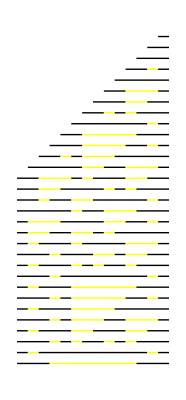

-Graphics-

```mathematica
list = Table[0, {30}];
list[[15]] = 1;
rules = {
{0,0,0} -> 0,
{0,0,1} -> 1, 
{0,1,0} -> 1, 
{0,1,1} -> 1, 
{1,0,0} -> 0, 
{1,0,1} -> 1,
{1,1,0} -> 1,
{1,1,1} -> 0
};
(*Chop up the list and apply the rules*)
Partition[list, 3, 1] /. rules;
(*Pad the list with zeros on both sides*)
Join[{0}, list, {0}];
(*Create a function to do this*)
step[seq_] := Join[{0}, Partition[seq, 3, 1] /. rules, {0}];
array = NestList[step, list, 30];

summarizedArray = {};

For[i = 1, i≤ Length[array], ++i,
	(* row i *)
	line = {};
	For[j=1, j≤ Length[array[[i]]], ++j,
		If[Length[line] == 0, (* init *)
			line = {i,j,i,j, array[[i,j]]}, 
		(*else: if value is the same as last line's value*)
			If[array[[i,j]] == line[[5]],
				line = {line[[1]], line[[2]], i,j, line[[5]]},
				(*else: new value --> store old line, start new line*)
				summarizedArray = Append[summarizedArray, line]; line = {i,j,i,j,array[[i,j]]}]
		]
	]
]
SubArrayToLine[a_] := (
	p1 = {a[[2]]-0.5, -a[[1]]};
	p2 = {a[[4]]+0.5, -a[[3]]};
	l = Line[{p1, p2}];
	Return[l];
)
FormattingOfLine[x_]:=(
	Return[ If[x == 0 , Yellow, Black]];
)

FormatRawLineList[x_]:=(
	formattedLines = {};
	For[k = 1, k ≤ Length[x],++k,
		formattedLines = Append[formattedLines, FormattingOfLine[x[[k,5]]]];
		formattedLines = Append[formattedLines, SubArrayToLine[x[[k]]]];
	];
	Return[formattedLines];
)

RemoveTrailingZeroLines[x_]:=(
	indicesToBeDropped = {};
	(*first element*)
	If[ x[[1,5]]==0 , indicesToBeDropped=Append[indicesToBeDropped, {1}], 0]
	(* rest *)
	For[i=2,i≤Length[x]-1,++i,
		(*look at neighbors left and right, same y value? *)
		If[    (x[[i,5]] == 0 && x[[i,1]] ≠ x[[i-1,1]])       (* is zero-line and leading *)
			|| (x[[i,5]] == 0 && x[[i,1]] ≠ x[[i+1,1]]),       (* is zero-line and trailing *)
			indicesToBeDropped=Append[indicesToBeDropped, {i}],
			0]
	]
	(* last element *)
	If[Last[x][[5]]==0 , indicesToBeDropped = Append[indicesToBeDropped,{Length[x]}], 0];
	Return[Delete[x, indicesToBeDropped]]
	
)
formattedLines = FormatRawLineList[summarizedArray];
(*Graphics[{ Thick, formattedLines}]*)
RemoveTrailingZeroLines[summarizedArray]
trimmed = FormatRawLineList[RemoveTrailingZeroLines[summarizedArray]];
Graphics[{ Thick, trimmed}]
ArrayPlot[array]
```

```mathematica
{1,1,1,14,0}
```

{1,1,1,14,0}